## Introduction

Try and find fixed points “by hand” when  E > 0

### Ideas

1. Sub trig to polynomial: x=sin θ, cosθ=±√(1-x^2) etc
2. Search for solutions with x1=x2, θ1=θ2 etc

## Attempt 1

### ODEs

```mathematica
Clear[b,j,k]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Find fp

#### Move from trig --> polynomail

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->√(1-x^2),
Cos[xm]->y,
Sin[xm]->√(1-y^2),
Cos[θp]->w,
Sin[θp]->√(1-w^2),
Cos[θm]->z,
Sin[θm]->√(1-z^2)
};

TableForm[es]
es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

e-x √(1-y^2)
-√(1-x^2) y-k y √(1-y^2) z^2+k y √(1-y^2) (1-z^2)
e-w √(1-z^2)
-√(1-w^2) z-k y^2 z √(1-z^2)+k (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination one by om

### Solve one by one

#### First FP

```mathematica
xsol=Solve[es1[[1]]==0,x][[1,1]]
```

x→e/(√(1-y^2))

```mathematica
zsol=(Solve[(es1[[2]]/.xsol)==0,z]//Simplify)[[1,1]]
```

z→-(ⅈ √(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))/(√2 √k (1-y^2)^(1/4))

```mathematica
wsol=Solve[es1[[3]]==0,w][[1,1]]
```

w→e/(√(1-z^2))

```mathematica
temp=es1[[4]]/.xsol/.zsol/.wsol/.zsol//Simplify
```

(ⅈ √(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))) (√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)))))/(2 √k (1-y^2)^(1/4))

Need to clean this up

```mathematica
temp1=Numerator[temp]
```

ⅈ √(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))) (√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2))))

Now I set both factors equal to zero and find the fp

```mathematica
temp2=temp1[[2]]
```

√(-k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))

```mathematica
ysol1=FullSimplify[Solve[temp2==0,y],{e>0}]
```

{{y→-(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)},{y→(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)},{y→-(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)},{y→(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)}}

Ok, so here are some fixed points. Now the second term

```mathematica
$Assumptions={e>0};
```

```mathematica
xsol/.ysol1
```

{x→e/(√(1+(1-2 k^2+√(1-4 e^2 k^2))/(2 k^2))),x→e/(√(1+(1-2 k^2+√(1-4 e^2 k^2))/(2 k^2))),x→e/(√(1-(-1+2 k^2+√(1-4 e^2 k^2))/(2 k^2))),x→e/(√(1-(-1+2 k^2+√(1-4 e^2 k^2))/(2 k^2)))}

```mathematica
zsol/.ysol//Simplify
```

{z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)),z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)),z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4)),z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4))}

```mathematica
wsol/.zsol/.ysol//Simplify
```

{w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2)))),w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2)))),w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2)))),w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2))))}

```mathematica
ysol1//Flatten
```

{y→-(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2),y→(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2),y→-(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2),y→(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2)}

```mathematica
fp1={xsol/.ysol1,ysol1//Flatten,zsol/.ysol,wsol/.zsol/.ysol}ᵀ//Simplify;
TableForm[fp1]
```

x→(√2 e)/(√((1+√(1-4 e^2 k^2))/k^2)) | y→-(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)) | w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2))))
x→(√2 e)/(√((1+√(1-4 e^2 k^2))/k^2)) | y→(√(-(1-2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-√2 k √((1+√(1-4 e^2 k^2))/k^2)+2 √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1+√(1-4 e^2 k^2))/k^2)^(1/4)) | w→e/(√((1+√(1-4 e^2 k^2)+√2 k √((1+√(1-4 e^2 k^2))/k^2) √((1-2 e^2 k^2+√(1-4 e^2 k^2))/(1+√(1-4 e^2 k^2))))/(2+2 √(1-4 e^2 k^2))))
x→(√2 e)/(√((1-√(1-4 e^2 k^2))/k^2)) | y→-(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4)) | w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2))))
x→(√2 e)/(√((1-√(1-4 e^2 k^2))/k^2)) | y→(√((-1+2 k^2+√(1-4 e^2 k^2))/k^2))/(√2) | z→-(ⅈ √(-k √((2-2 √(1-4 e^2 k^2))/k^2)+2 √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2)))))/(2^(3/4) √k ((1-√(1-4 e^2 k^2))/k^2)^(1/4)) | w→(√2 e)/(√((-1+√(1-4 e^2 k^2)-k √((2-2 √(1-4 e^2 k^2))/k^2) √((-1+2 e^2 k^2+√(1-4 e^2 k^2))/(-1+√(1-4 e^2 k^2))))/(-1+√(1-4 e^2 k^2))))

Hmm, I was expecting some symmetry. But recall, this is just for one set of fixed points (and not *all*) fixed points.

```mathematica
subC={C[1]->0,C[2]->0,C[3]->0,C[4]->0};
Manipulate[
p1=ListPlot[{x,y}/.fp1/.subC/.k->k1/.e->e1,
PlotStyle->PointSize[Large],
AxesLabel->{"x1","x2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}},
ImageSize->Medium
];

p2=ListPlot[{w,z}/.fp1/.subC/.k->k1/.e->e1,
PlotStyle->PointSize[Large],
AxesLabel->{"θ1","θ2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}},
ImageSize->Medium
];

Grid[{{p1,p2}}]
,
{{k1,0.01},-5,5},{e1,0.01,1}
]
```

#### Rest of FP

```mathematica
temp3=temp1[[3]]
```

√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)))

Ok, this one is hard. Let me plot it first

```mathematica
Manipulate[Plot[temp3/.{k->k1,e->e1},{y,-3,3},AxesOrigin->{0,0}],{k1,-3,3},{e1,0,3}]
```

Hmm... so there are two real solution, it seems.

```mathematica
Solve[temp3==0,y]
```

$Aborted

I’ll have to try and clean it first by hand

```mathematica
Simplify[Together[temp3]]
```

√2 √(((1-2 e^2) k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)+√((-1+e^2+y^2)/(-1+y^2))))+k (-1+2 y^2) √(1+(√((-1+e^2+y^2)/(-1+y^2)))/(k √(1-y^2)))

Can I turn this into  a polynomial in y?

```mathematica
ysol2=FullSimplify[Solve[temp1[[3]]==0,y],{e>0}]
```

$Aborted

## Attempt 2

### ODEs

```mathematica
Clear[b,j,k]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Find fp

#### Move from trig --> polynomail

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->√(1-x^2),
Cos[xm]->y,
Sin[xm]->√(1-y^2),
Cos[θp]->w,
Sin[θp]->√(1-w^2),
Cos[θm]->z,
Sin[θm]->√(1-z^2)
};

TableForm[es]
es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

e-x √(1-y^2)
-√(1-x^2) y-k y √(1-y^2) z^2+k y √(1-y^2) (1-z^2)
e-w √(1-z^2)
-√(1-w^2) z-k y^2 z √(1-z^2)+k (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination x and w easily. I’ll do that first

### Solve one by one

#### First FP

```mathematica
xwsol=Solve[es1[[{1,3}]]==0,{x,w}]
```

{{x→e/(√(1-y^2)),w→e/(√(1-z^2))}}

```mathematica
es2=(es1[[{2,4}]]/.xwsol//Simplify)[[1]]
```

{-y (√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)),-z (k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2)))}

What geometric shape in the (y,z) plane is this?

```mathematica
Manipulate[
ContourPlot[{(es2[[1]]/.k->k1/.e->e1)==0,(es2[[2]]/.k->2/.e->0.5)==0},{y,-3,3},{z,-3,3}],
{k1,0,3},{e1,0,3}
]
```

Huh. So the shapes are complicated. Are they elliptical curves? I’m not sure.. I can see y=z=0 is always a solution.

```mathematica
es2
```

{-y (√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)),-z (k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2)))}

Let’s see if Mma can do it

```mathematica
Solve[es2==0,{y,z}]
```

$Aborted

No. I’ll peel of the (y,z).

```mathematica
es2[[1,3]]
```

√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)

```mathematica
es3={es2[[1,3]],es2[[2,3]]}//Simplify
```

{√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2),k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2))}

```mathematica
temp=es3[[1]]
```

√((-1+e^2+y^2)/(-1+y^2))+k √(1-y^2) (-1+2 z^2)

Since the RHS is zero, I can square both terms individually and then subtradct them again. That is, X+Y=0 → X=-Y→X^2=Y^2→X^2-Y^2=

```mathematica
temp1=(temp[[1]])^2-(temp[[2]])^2
```

(-1+e^2+y^2)/(-1+y^2)-k^2 (1-y^2) (-1+2 z^2)^2

```mathematica
temp2=Numerator[Together[temp1]]
```

-1+e^2+k^2+y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4

So a mixed 4th order. Can I simplify it?

```mathematica
temp3=Simplify[temp2]
```

e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2)

Yes, that’s cleaner.. Now the other one

```mathematica
t=es3[[2]]
```

k (-1+2 y^2) √(1-z^2)+√((-1+e^2+z^2)/(-1+z^2))

```mathematica
t1=Numerator[Together[(t[[1]])^2-(t[[2]])^2]]//Simplify
```

-e^2-(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2))

```mathematica
esNew={temp3,t1};
```

```mathematica
Manipulate[
ContourPlot[{(esNew[[1]]/.k->k1/.e->e1)==0,(esNew[[2]]/.k->k1/.e->e1)==0},
{y,-3,3},{z,-3,3},
FrameLabel->{"y","z"},
LabelStyle->18,
PlotLabel->"{K,E} = "<>ToString[{k1,e1}]],
{{k1,2},0,3},{{e1,0.15},0,3}
]
```

Beautiful! We should include this is the paper, maybe. There’s symmetry in (z,y), as expect. Can see there are multiple fixed points, depending on (K,E).

```mathematica
esNew//TableForm
```

e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2)
-e^2-(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2))

You can see the E=0 solution will be (relatively) simple

```mathematica
Solve[(esNew/.e->0)==0,{y,z}]
```

{{y→-1,z→-(√(-1+k^2))/k},{y→-1,z→(√(-1+k^2))/k},{y→1,z→-(√(-1+k^2))/k},{y→1,z→(√(-1+k^2))/k},24,{y→-1,z→1},{y→1,z→1},{y→-(√(-1+k^2))/k,z→1},{y→(√(-1+k^2))/k,z→1}}
 |  |  |  |

Ok, I can see the are the new fixed points. When I turn E>0... it will be difficult.

```mathematica
esNew[[1]]
```

e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2)

```mathematica
FindRoot[esNew/.{k->0.55,e->0.5},{y,1},{z,2}]
```

{y→0.863294,z→0.863294}

Maybe there’s a solution with z=y?

#### Look for solution with z=y

```mathematica
esNew={e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2),-e^2-(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2))};
temp5=Collect[Expand[esNew[[1]]/.z->y],y,Simplify]
```

-1+e^2+k^2+(1-6 k^2) y^2+13 k^2 y^4-12 k^2 y^6+4 k^2 y^8

So this is 4th order in y^2 which should have a solution

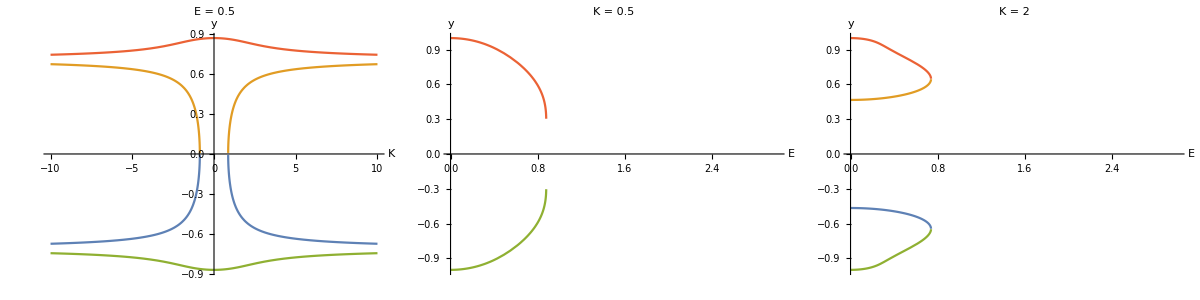

```mathematica
ysolSymmetric=Simplify[Solve[temp5==0,y],Assumptions->{e>0}];
p1=Plot[y/.ysolSymmetric/.e->0.5//Evaluate,{k,-10,10},AxesLabel->{"K","y"},LabelStyle->15,ImageSize->Medium,PlotLabel->"E = 0.5"];
p2=Plot[y/.ysolSymmetric/.k->0.5//Evaluate,{e,0,3},AxesLabel->{"E","y"},LabelStyle->15,ImageSize->Medium,PlotLabel->"K = 0.5"];
p3=Plot[y/.ysolSymmetric/.k->2//Evaluate,{e,0,3},AxesLabel->{"E","y"},LabelStyle->15,ImageSize->Medium, PlotLabel->"K = 2"];
Grid[{{p1,p2,p3}}]
```

Ok, I can see the bifurcation structure here. I think I may be able to infer

## Attempt 3 -- think I solved them exact

### ODEs

```mathematica
Clear[b,j,k,e]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Trig --> polynomial

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points. 
Note I’m defining p=±1. As we see, eventually only p^2 appears, so it effectively cancels outs.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->p √(1-x^2),
Cos[xm]->y,
Sin[xm]->p √(1-y^2),
Cos[θp]->w,
Sin[θp]->p √(1-w^2),
Cos[θm]->z,
Sin[θm]->p √(1-z^2)
};

TableForm[es]
es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

e-p x √(1-y^2)
-p √(1-x^2) y-k p y √(1-y^2) z^2+k p^3 y √(1-y^2) (1-z^2)
e-p w √(1-z^2)
-p √(1-w^2) z-k p y^2 z √(1-z^2)+k p^3 (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination x and w easily. I’ll do that first

### Eliminate first two

```mathematica
xwsol=Solve[es1[[{1,3}]]==0,{x,w}]
```

{{x→e/(p √(1-y^2)),w→e/(p √(1-z^2))}}

```mathematica
es2=(es1[[{2,4}]]/.xwsol//Simplify)[[1]]
```

{p y (-√(1+e^2/(p^2 (-1+y^2)))-k √(1-y^2) (z^2+p^2 (-1+z^2))),p z (-k (y^2+p^2 (-1+y^2)) √(1-z^2)-√(1+e^2/(p^2 (-1+z^2))))}

Get rid of the p=± 1

```mathematica
es3=Expand[es2^2/.{p^2->1,p^2->1}]/.p->1//Together//Numerator;
es3//TableForm
```

-y^2+e^2 y^2-k^2 y^2+y^4+2 k^2 y^4-k^2 y^6+2 k y^2 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2))-2 k y^4 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2))+4 k^2 y^2 z^2-8 k^2 y^4 z^2+4 k^2 y^6 z^2-4 k y^2 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2)) z^2+4 k y^4 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2)) z^2-4 k^2 y^2 z^4+8 k^2 y^4 z^4-4 k^2 y^6 z^4
-z^2+e^2 z^2-k^2 z^2+4 k^2 y^2 z^2-4 k^2 y^4 z^2+z^4+2 k^2 z^4-8 k^2 y^2 z^4+8 k^2 y^4 z^4-k^2 z^6+4 k^2 y^2 z^6-4 k^2 y^4 z^6+2 k z^2 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))-4 k y^2 z^2 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))-2 k z^4 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))+4 k y^2 z^4 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))

### Eliminate the sqrts

```mathematica
e2=es3[[1]]/.√(1-y^2) √((-1+e^2+y^2)/(-1+y^2))->X
```

-y^2+e^2 y^2-k^2 y^2+2 k X y^2+y^4+2 k^2 y^4-2 k X y^4-k^2 y^6+4 k^2 y^2 z^2-4 k X y^2 z^2-8 k^2 y^4 z^2+4 k X y^4 z^2+4 k^2 y^6 z^2-4 k^2 y^2 z^4+8 k^2 y^4 z^4-4 k^2 y^6 z^4

```mathematica
Solve[e2==0,X]
```

{{X→(1-e^2+k^2-y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+y^2) (-1+2 z^2))}}

Do this bit by hand

```mathematica
e3=Simplify[Numerator[Together[((1-e^2+k^2-y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+y^2) (-1+2 z^2)))^2-(√(1-y^2) √((-1+e^2+y^2)/(-1+y^2)))^2]]]
```

(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2

I know the other equation is the mirror symmetry of (y,z) --> (z,y)

```mathematica
e4=e3/.{y->z,z->y}
```

(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2

```mathematica
est={e3,e4}//Simplify
```

{(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2,(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2}

So these are my equations. Can I solve these exactly?

```mathematica
sols=Solve[est==0,{y,z}]
```

{{y→-√(3/4-1/(2 k^2)+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(-16 e^2+k^2))-1/(k √(-16 e^2+k^2)))),z→-(√(-16-64 e^2+80 e^4+40 k^2+148+16 k^8 (3/4-1/1+1-1/2 √1)^7+64 e^2 k^8 (3/4-1/(2 k^2)+(√1)/(4 k)-1/2 √(1/k^4+6))^7-1024 e^4 k^8 (3/4-1/(2 k^2)+(√(1+1))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(1+1))-1/(k √(-16 e^2+k^2))))^7))/(√(-16 e^4 k^2+20 e^4 k^4-64 e^6 k^4-4 e^4 k^6+16 e^6 k^6))},{y→-√(3/4-1/1+1-1/2 √(1/k^4+6)),z→1},28,{1},{y→√(3/4+1/2 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(5+1)^(1/3)/(12 k^2))+1/2 √(1/6-(-12+48 e^2+k^2)/(12 (5+6 √3 √1)^(1/3))-(5+6 √3 √1)^(1/3)/(12 k^2)+(-12-(2 (1-6 k^2))/k^2)/(4 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(1)^(1/3)/(12 k^2))))),z→(√1)/(√(-16 e^4 k^2+5+16 e^6 k^6))}}
 |  |  |  |

Sweet. Let’s plot them

### Plot results

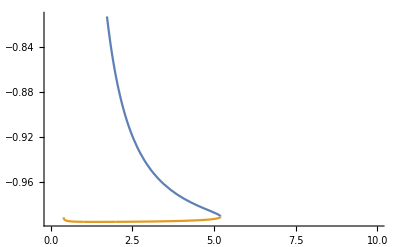
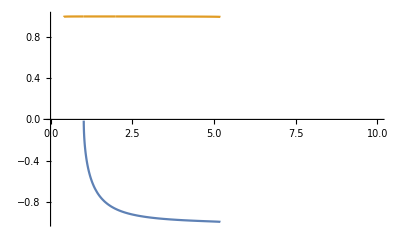
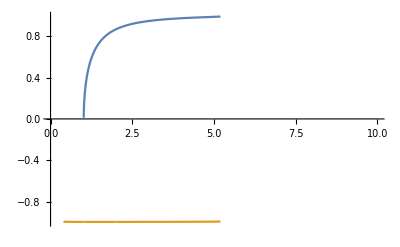
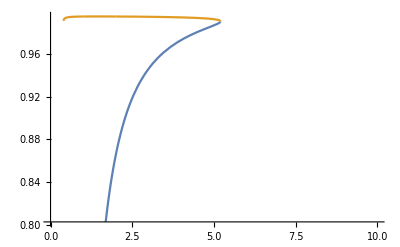
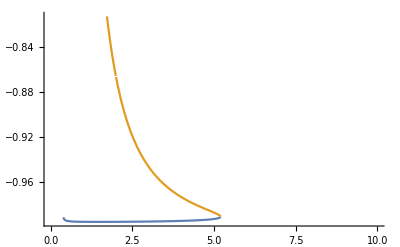
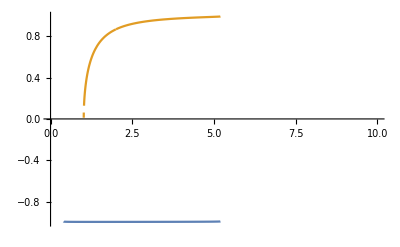
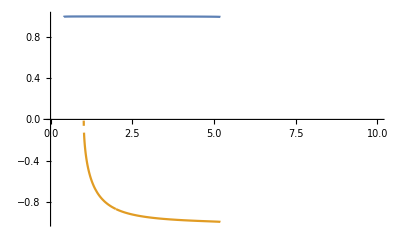
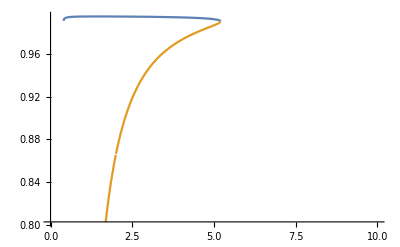

```mathematica
ParallelTable[
Plot[{y,z}/.sols[[i]]/.e->0.1//Evaluate,{k,0,10}],
{i,1,Length[sols]}
]
```

### Gather results

#### Look at just 1

```mathematica
solsFinal=Table[{Flatten[xwsol/.p->1],sols[[i]]}//Flatten,{i,1,4}];
TableForm[solsFinal]
```

1
 |  |  |  |

{Cos[xp], Cos[xm], Cos[θp] Cos[θm]} == {x, y, w, z}

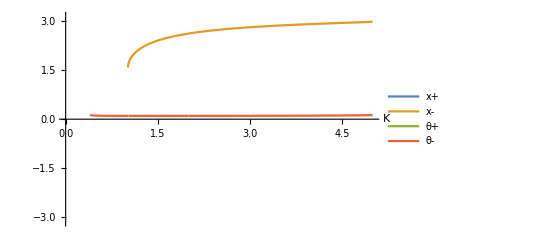

```mathematica
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[2]];
Plot[{xp,xm,θp,θm}/.e->0.1//Evaluate,{k,0,5},PlotLegends->{"x+","x-","θ+","θ-"},PlotRange->{-π,π},AxesLabel->{"K"},LabelStyle->15]
```

#### Gather all

```mathematica
solsFinal=Table[{Flatten[xwsol/.sols[[i]]/.p->1],sols[[i]]}//Flatten,{i,1,Length[sols]}];
TableForm[solsFinal]
```

1
 |  |  |  |

Power::infy: Infinite expression 1/(√0.) encountered.

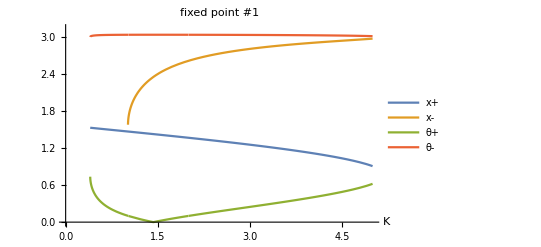
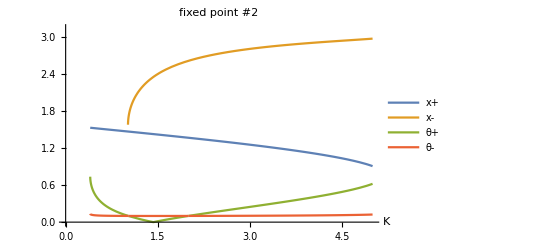
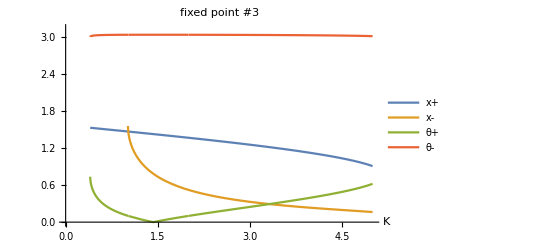
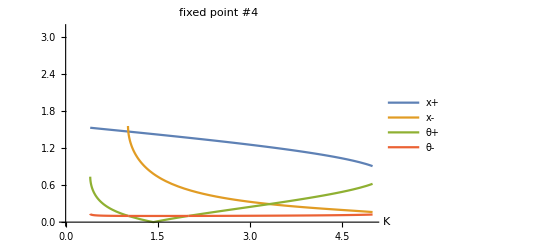
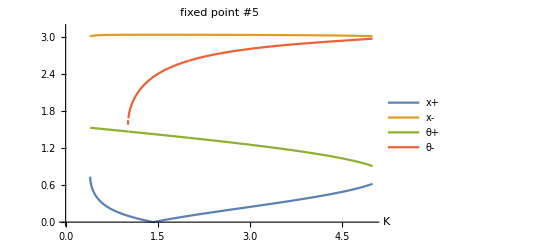
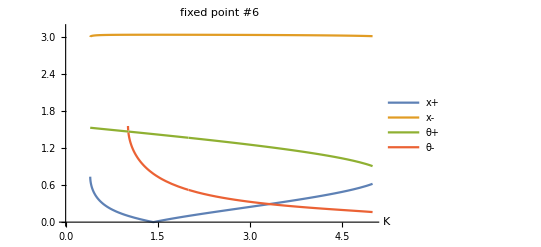
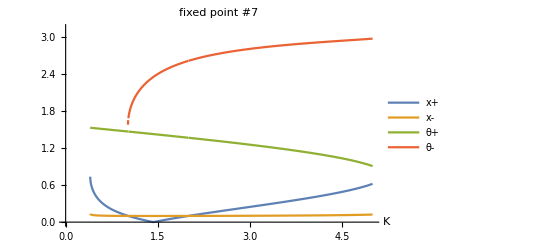
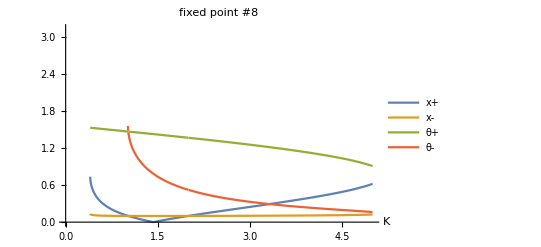
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  |

```mathematica
Clear[xp,xm,θp,θm,e,k];
figs=Table[
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Plot[{xp,xm,θp,θm}/.e->0.1//Evaluate,{k,0,5},PlotLegends->{"x+","x-","θ+","θ-"},PlotRange->{0,π},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"fixed point #" <>ToString[i]],
{i,1,Length[solsFinal]}
];

Grid[Partition[figs,UpTo[5]]]
```

### Find expressions for S_± -- work in progress.

#### Attempt 1

S_+= cos(x)

```mathematica
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
subY1={y->√y1,z->√z1};
xwsol={x->e/(p √(1-y^2)),w->e/(p √(1-z^2))}/.subY1//Flatten;
temp={x,√y1,√z1,w}/.xwsol/.sols[[1]]/.p->1//Simplify;
subSol={x,y,z,w};
subFinal=Table[subSol[[i]]->temp[[i]],{i,1,4}];
S=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
Sfinal=(S/.subX1//TrigExpand)/.sub/.p->1/.subFinal//Simplify;
FullSimplify[Expand[Sfinal]]
```

ⅇ^(ⅈ (xp-θp)) Cos[xm-θm]

```mathematica
Wp=FullSimplify[TrigExpand[ExpToTrig[S/.subX1]]/.sub/.p->1/.subFinal,Assumptions->e>0]//Simplify;
```

```mathematica
Wp/.
```

```mathematica
Wp/.e->0.5/.k->2
```

0.683013+0.683013 ⅈ

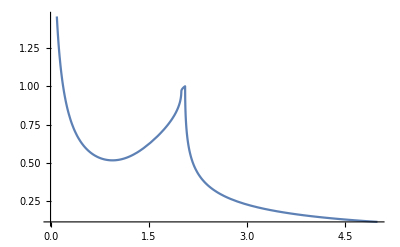

```mathematica
Plot[Abs[Wp]/.e->0.5,{k,0,5}]
```

#### Attempt 2

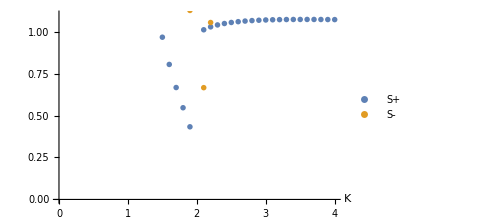

```mathematica
i=6;
Clear[x1,x2,θ1,θ2,xp,xm,θp,θm]
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
Sp=(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)])/2;
Sm=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
{Sp,Sm}={TrigExpand[ExpToTrig[Sp/.subX1]],TrigExpand[ExpToTrig[Sm/.subX1]]};
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Spdata=Table[{k,Sp/.e->0.5},{k,0.1,4,0.1}]//Quiet;
Smdata=Table[{k,Sm/.e->0.5},{k,0.1,4,0.1}]//Quiet;
p1=ListPlot[{Spdata//Abs,Smdata//Abs},AxesLabel->{"K"},LabelStyle->15,ImageSize->Medium,PlotLegends->{"S+","S-"},PlotRange->{0,1.1}]
```

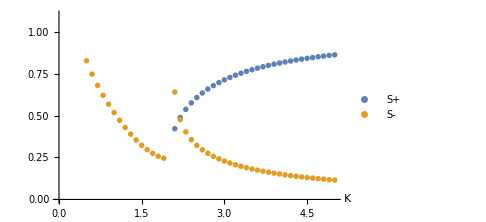
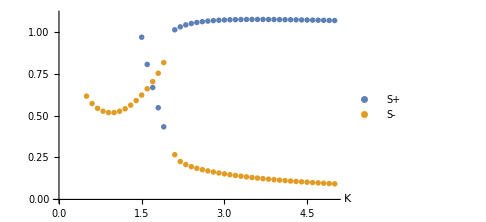
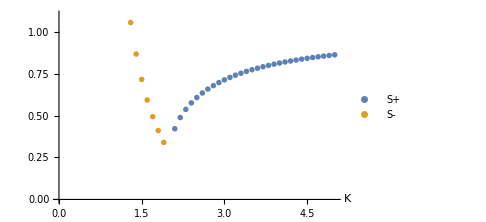
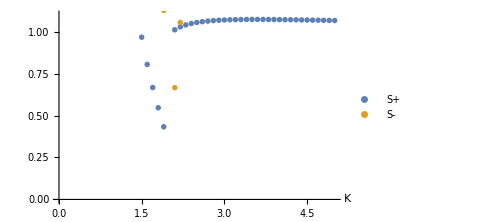
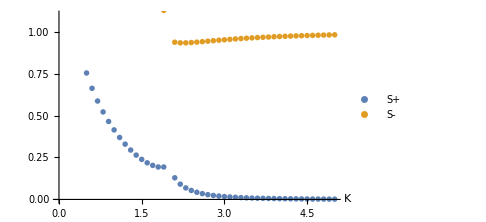
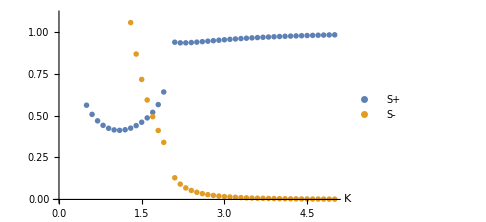
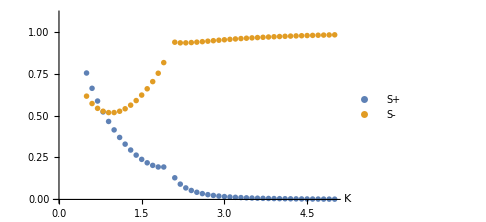
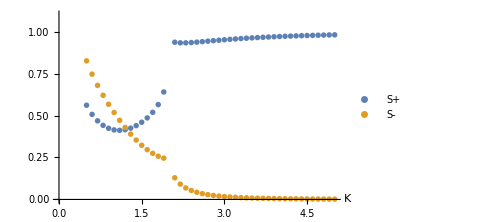
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Clear[x1,x2,θ1,θ2,xp,xm,θp,θm];
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
Sp=(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)])/2;
Sm=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
{Sp,Sm}={TrigExpand[ExpToTrig[Sp/.subX1]],TrigExpand[ExpToTrig[Sm/.subX1]]};
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Spdata=Table[{k,Sp/.e->0.5},{k,0.5,5,0.1}]//Quiet;
Smdata=Table[{k,Sm/.e->0.5},{k,0.5,5,0.1}]//Quiet;
ListPlot[{Spdata//Abs,Smdata//Abs},AxesLabel->{"K"},LabelStyle->15,ImageSize->Medium,PlotLegends->{"S+","S-"},PlotRange->{Automatic,{0,1.1}}],
{i,1,Length[solsFinal]}
]
```

```mathematica
Length[solsFinal]
```

32

## Attempt 4

### ODEs

#### Original

```mathematica
esOriginal={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]+j/2 Sin[x1-x2]Cos[θ1-θ2],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]+k/2 Sin[θ1-θ2]Cos[x1-x2]
}/.{α1->0,α2->π};
TableForm[esOriginal]
```

e-b Sin[x1]-1/2 j Cos[θ1-θ2] Sin[x1-x2]
e+1/2 j Cos[θ1-θ2] Sin[x1-x2]+b Sin[x2]
e-b Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
e+1/2 k Cos[x1-x2] Sin[θ1-θ2]+b Sin[θ2]

```mathematica
(esOriginal[[1]]-esOriginal[[2]])/2//Simplify
```

1/2 (-b Sin[x1]-j Cos[θ1-θ2] Sin[x1-x2]-b Sin[x2])

```mathematica
(esOriginal[[3]]+esOriginal[[4]])/2//Simplify
```

e-1/2 b Sin[θ1]+1/2 b Sin[θ2]

```mathematica
TrigFactor[-b Sin[x1]-b Sin[x2]]
```

-2 b Cos[x1/2-x2/2] Sin[x1/2+x2/2]

```mathematica
eqns={
e-b Cos[x1/2+x2/2] Sin[x1/2-x2/2],
- b Cos[x1/2-x2/2] Sin[x1/2+x2/2]-j/2  Cos[θ1-θ2] Sin[x1-x2],
e+b Cos[θ1/2+θ2/2] Sin[θ1/2-θ2/2],
- b Cos[θ1/2-θ2/2] Sin[θ1/2+θ2/2]-j/2  Cos[x1-x2] Sin[θ1-θ2]
};
TableForm[eqns]
```

e-b Cos[x1/2+x2/2] Sin[x1/2-x2/2]
-1/2 j Cos[θ1-θ2] Sin[x1-x2]-b Cos[x1/2-x2/2] Sin[x1/2+x2/2]
e+b Cos[θ1/2+θ2/2] Sin[θ1/2-θ2/2]
-1/2 j Cos[x1-x2] Sin[θ1-θ2]-b Cos[θ1/2-θ2/2] Sin[θ1/2+θ2/2]

#### In (xp,xm,..) coords

```mathematica
Clear[b,j,k,e,xp,xm,θp,θm];
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Trig --> polynomial

Here I’m only including one branch of fixed points. So I’m searching for *a* fixed point -- not *all* fixed points. 
Note I’m defining p=±1. As we see, eventually only p^2 appears, so it effectively cancels outs.

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->p √(1-x^2),
Cos[xm]->y,
Sin[xm]->p √(1-y^2),
Cos[θp]->w,
Sin[θp]->p √(1-w^2),
Cos[θm]->z,
Sin[θm]->p √(1-z^2)
};

es1=TrigExpand[es]/.sub;
TableForm[es1]
```

e-p x √(1-y^2)
-p √(1-x^2) y-k p y √(1-y^2) z^2+k p^3 y √(1-y^2) (1-z^2)
e-p w √(1-z^2)
-p √(1-w^2) z-k p y^2 z √(1-z^2)+k p^3 (1-y^2) z √(1-z^2)

Looking at these, I can do the elimination x and w easily. I’ll do that first

### Eliminate first two

```mathematica
xwsol=Solve[es1[[{1,3}]]==0,{x,w}]
```

{{x→e/(p √(1-y^2)),w→e/(p √(1-z^2))}}

```mathematica
es2=(es1[[{2,4}]]/.xwsol//Simplify)[[1]]
```

{p y (-√(1+e^2/(p^2 (-1+y^2)))-k √(1-y^2) (z^2+p^2 (-1+z^2))),p z (-k (y^2+p^2 (-1+y^2)) √(1-z^2)-√(1+e^2/(p^2 (-1+z^2))))}

Get rid of the p=± 1

```mathematica
es3=Expand[es2^2/.{p^2->1,p^2->1}]/.p->1//Together//Numerator;
es3//TableForm
```

-y^2+e^2 y^2-k^2 y^2+y^4+2 k^2 y^4-k^2 y^6+2 k y^2 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2))-2 k y^4 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2))+4 k^2 y^2 z^2-8 k^2 y^4 z^2+4 k^2 y^6 z^2-4 k y^2 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2)) z^2+4 k y^4 √(1-y^2) √((-1+e^2+y^2)/(-1+y^2)) z^2-4 k^2 y^2 z^4+8 k^2 y^4 z^4-4 k^2 y^6 z^4
-z^2+e^2 z^2-k^2 z^2+4 k^2 y^2 z^2-4 k^2 y^4 z^2+z^4+2 k^2 z^4-8 k^2 y^2 z^4+8 k^2 y^4 z^4-k^2 z^6+4 k^2 y^2 z^6-4 k^2 y^4 z^6+2 k z^2 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))-4 k y^2 z^2 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))-2 k z^4 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))+4 k y^2 z^4 √(1-z^2) √((-1+e^2+z^2)/(-1+z^2))

### Eliminate the sqrts

#### Eq 3

```mathematica
e2=es3[[1]]/.√(1-y^2) √((-1+e^2+y^2)/(-1+y^2))->X
```

-y^2+e^2 y^2-k^2 y^2+2 k X y^2+y^4+2 k^2 y^4-2 k X y^4-k^2 y^6+4 k^2 y^2 z^2-4 k X y^2 z^2-8 k^2 y^4 z^2+4 k X y^4 z^2+4 k^2 y^6 z^2-4 k^2 y^2 z^4+8 k^2 y^4 z^4-4 k^2 y^6 z^4

```mathematica
Solve[e2==0,X]
```

{{X→(1-e^2+k^2-y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+y^2) (-1+2 z^2))}}

Do this bit by hand

```mathematica
e3=Simplify[Numerator[Together[((1-e^2+k^2-y^2-2 k^2 y^2+k^2 y^4-4 k^2 z^2+8 k^2 y^2 z^2-4 k^2 y^4 z^2+4 k^2 z^4-8 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+y^2) (-1+2 z^2)))^2-(√(1-y^2) √((-1+e^2+y^2)/(-1+y^2)))^2]]]
```

(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2

I know the other equation is the mirror symmetry of (y,z) --> (z,y)

#### Eq 4 -- same by symmetry

```mathematica
e4=es3[[2]]/.√(1-z^2) √((-1+e^2+z^2)/(-1+z^2))->Y
```

-z^2+e^2 z^2-k^2 z^2+4 k^2 y^2 z^2-4 k^2 y^4 z^2+2 k Y z^2-4 k y^2 Y z^2+z^4+2 k^2 z^4-8 k^2 y^2 z^4+8 k^2 y^4 z^4-2 k Y z^4+4 k y^2 Y z^4-k^2 z^6+4 k^2 y^2 z^6-4 k^2 y^4 z^6

```mathematica
Solve[e4==0,Y]
```

{{Y→(1-e^2+k^2-4 k^2 y^2+4 k^2 y^4-z^2-2 k^2 z^2+8 k^2 y^2 z^2-8 k^2 y^4 z^2+k^2 z^4-4 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+2 y^2) (-1+z^2))}}

```mathematica
e5=((1-e^2+k^2-4 k^2 y^2+4 k^2 y^4-z^2-2 k^2 z^2+8 k^2 y^2 z^2-8 k^2 y^4 z^2+k^2 z^4-4 k^2 y^2 z^4+4 k^2 y^4 z^4)/(2 k (-1+2 y^2) (-1+z^2)))^2-(√(1-z^2) √((-1+e^2+z^2)/(-1+z^2)))^2//Simplify//Together//Numerator//Simplify
```

(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2

#### Collect

```mathematica
eqns={e3,e5};
TableForm[eqns]
```

(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2
(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2

So they are symmetric

```mathematica
est={e3,e4}//Simplify
```

{(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2,(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2}

So these are my equations. Can I solve these exactly?

```mathematica
sols=Solve[eqns==0,{y,z}]
```

{{y→-√(3/4-1/(2 k^2)+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(-16 e^2+k^2))-1/(k √(-16 e^2+k^2)))),z→-(√(-16-64 e^2+80 e^4+40 k^2+148+16 k^8 (3/4-1/1+1-1/2 √1)^7+64 e^2 k^8 (3/4-1/(2 k^2)+(√1)/(4 k)-1/2 √(1/k^4+6))^7-1024 e^4 k^8 (3/4-1/(2 k^2)+(√(1+1))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(1+1))-1/(k √(-16 e^2+k^2))))^7))/(√(-16 e^4 k^2+20 e^4 k^4-64 e^6 k^4-4 e^4 k^6+16 e^6 k^6))},{y→-√(3/4-1/1+1-1/2 √(1/k^4+6)),z→1},28,{1},{y→√(3/4+1/2 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(5+1)^(1/3)/(12 k^2))+1/2 √(1/6-(-12+48 e^2+k^2)/(12 (5+6 √3 √1)^(1/3))-(5+6 √3 √1)^(1/3)/(12 k^2)+(-12-(2 (1-6 k^2))/k^2)/(4 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(1)^(1/3)/(12 k^2))))),z→(√1)/(√(-16 e^4 k^2+5+16 e^6 k^6))}}
 |  |  |  |

Sweet. Let’s plot them

#### Verify sols

```mathematica
Length[sols]
```

32

```mathematica
xwsol
```

{{x→e/(p √(1-y^2)),w→e/(p √(1-z^2))}}

```mathematica
eqns
```

{(e^2+(-1+y^2) (1+k^2 (-1+y^2) (1-2 z^2)^2))^2,(e^2+(-1+z^2) (1+k^2 (1-2 y^2)^2 (-1+z^2)))^2}

```mathematica
eqns/.sols[[1]]//Simplify
```

{0,0}

```mathematica
Table[eqns/.p->1/.sols[[i]]/.e->1/.k->3//N//Chop,{i,1,Length[sols]}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

Looks good

```mathematica
Table[eqns/.sols[[i]]/.e->1/.k->3//N//Chop,{i,1,Length[sols]}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

And its invarient for p too

#### Convert back to trig

```mathematica
sub//TableForm
```

Cos[xp]→x
Sin[xp]→p √(1-x^2)
Cos[xm]→y
Sin[xm]→p √(1-y^2)
Cos[θp]→w
Sin[θp]→p √(1-w^2)
Cos[θm]→z
Sin[θm]→p √(1-z^2)

```mathematica
subs1={xp->ArcCos[x],xm->ArcCos[y],θp->ArcCos[w],θm->ArcCos[z]}
```

{xp→ArcCos[x],xm→ArcCos[y],θp→ArcCos[w],θm→ArcCos[z]}

```mathematica
temp=subs1/.xwsol//Flatten/.sols[[1]]
```

{xp→ArcCos[e/(p √(1-y^2))],xm→ArcCos[y],θp→ArcCos[e/(p √(1-z^2))],θm→ArcCos[z]}

```mathematica
solPoly=temp/.sols[[1]]//Simplify
```

{xp→ArcCos[(2 e)/(√((2+k^2-k √(-16 e^2+k^2)+2 k^2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))/k^2) p)],xm→ArcCos[-1/2 √(3-2/k^2+(√(-16 e^2+k^2))/k-2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))],θp→ArcCos[(2 e)/(√((2+k^2-k √(-16 e^2+k^2)-2 k^2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))/k^2) p)],θm→ArcCos[-(√(e^4 (-4+k^2) (1+(-1+4 e^2) k^2) (-2+k √(-16 e^2+k^2)+k^2 (3+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)))))/(2 √(e^4 k^2 (-4+k^2) (1+(-1+4 e^2) k^2)))]}

```mathematica
temp=TrigExpand[es[[2]]]/.sub//Simplify/.sols[[1]]
```

p y (-√(1-x^2)-k √(1-y^2) (z^2+p^2 (-1+z^2)))

```mathematica
((temp/.xwsol)[[1]])/.sols[[1]]/.e->2/.k->5/.p->-1//N
```

-3.92619+2.13948 ⅈ

```mathematica
sub
```

{Cos[xp]→x,Sin[xp]→p √(1-x^2),Cos[xm]→y,Sin[xm]→p √(1-y^2),Cos[θp]→w,Sin[θp]→p √(1-w^2),Cos[θm]→z,Sin[θm]→p √(1-z^2)}

```mathematica
es/.solPoly/.p->1//Simplify
```

{0,1/2 √(3-2/k^2+(√(-16 e^2+k^2))/k-2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)) √(1-(4 e^2 k^2)/(2-k √(-16 e^2+k^2)+k^2 (1+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))))-1/2 k Cos[2 ArcCos[-(√(e^4 (-4+k^2) (1+(-1+4 e^2) k^2) (-2+k √(-16 e^2+k^2)+k^2 (3+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)))))/(2 √(e^4 k^2 (-4+k^2) (1+(-1+4 e^2) k^2)))]] Sin[2 ArcCos[-1/2 √(3-2/k^2+(√(-16 e^2+k^2))/k-2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))]],0,(√(e^4 (-4+k^2) (1+(-1+4 e^2) k^2) (-2+k √(-16 e^2+k^2)+k^2 (3+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)))) √(1+(4 e^2 k^2)/(-2+k √(-16 e^2+k^2)+k^2 (-1+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)))))/(2 √(e^4 k^2 (-4+k^2) (1+(-1+4 e^2) k^2)))-1/2 k Cos[2 ArcCos[-1/2 √(3-2/k^2+(√(-16 e^2+k^2))/k-2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))]] Sin[2 ArcCos[-(√(e^4 (-4+k^2) (1+(-1+4 e^2) k^2) (-2+k √(-16 e^2+k^2)+k^2 (3+2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4)))))/(2 √(e^4 k^2 (-4+k^2) (1+(-1+4 e^2) k^2)))]]}

Maybe I should do express in terms of cos xp, cos xm etc.

```mathematica
xwsol
```

{{x→e/(p √(1-y^2)),w→e/(p √(1-z^2))}}

```mathematica
y/.sols/.e->2/.k->5//N//DeleteDuplicates//TableForm
```

-0.925535-0.377818 ⅈ
0.925535+0.377818 ⅈ
-0.864873+0.0432826 ⅈ
0.864873-0.0432826 ⅈ
-0.925535+0.377818 ⅈ
0.925535-0.377818 ⅈ
-0.864873-0.0432826 ⅈ
0.864873+0.0432826 ⅈ
-0.650303+0.194049 ⅈ
0.650303-0.194049 ⅈ
-0.650303-0.194049 ⅈ
0.650303+0.194049 ⅈ
-1.06389+0.130754 ⅈ
1.06389-0.130754 ⅈ
-1.06389-0.130754 ⅈ
1.06389+0.130754 ⅈ

They there’s 4 pairs, I think.

```mathematica
y/.sols[[1]]//Simplify
```

-1/2 √(3-2/k^2+(√(-16 e^2+k^2))/k-2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))

```mathematica
y/.sols[[3]]//Simplify
```

1/2 √(3-2/k^2+(√(-16 e^2+k^2))/k-2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))

```mathematica
e/(p √(1-y^2))/.sols[[1]]//Simplify
```

(2 e)/(√((2+k^2-k √(-16 e^2+k^2)+2 k^2 √((1+k^2-4 e^2 k^2-k √(-16 e^2+k^2))/k^4))/k^2) p)

```mathematica
2+2
```

4

### Plot results

```mathematica
ParallelTable[
Plot[{y,z}/.sols[[i]]/.e->0.1//Evaluate,{k,0,10}],
{i,1,Length[sols]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Gather results

#### Look at just 1

```mathematica
solsFinal=Table[{Flatten[xwsol/.p->1],sols[[i]]}//Flatten,{i,1,4}];
TableForm[solsFinal]
```

1
 |  |  |  |

{Cos[xp], Cos[xm], Cos[θp] Cos[θm]} == {x, y, w, z}

```mathematica
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[2]];
Plot[{xp,xm,θp,θm}/.e->0.1//Evaluate,{k,0,5},PlotLegends->{"x+","x-","θ+","θ-"},PlotRange->{-π,π},AxesLabel->{"K"},LabelStyle->15]
```

-Graphics-

#### Gather all

```mathematica
solsFinal=Table[{Flatten[xwsol/.sols[[i]]/.p->1],sols[[i]]}//Flatten,{i,1,Length[sols]}];
TableForm[solsFinal]
```

1
 |  |  |  |

```mathematica
Clear[xp,xm,θp,θm,e,k];
figs=Table[
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Plot[{xp,xm,θp,θm}/.e->0.1//Evaluate,{k,0,5},PlotLegends->{"x+","x-","θ+","θ-"},PlotRange->{0,π},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"fixed point #" <>ToString[i]],
{i,1,Length[solsFinal]}
];

Grid[Partition[figs,UpTo[5]]]
```

Power::infy: Infinite expression 1/(√0.) encountered.

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  |

### Find expressions for S_± -- work in progress.

#### Attempt 1

S_+= cos(x)

```mathematica
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
subY1={y->√y1,z->√z1};
xwsol={x->e/(p √(1-y^2)),w->e/(p √(1-z^2))}/.subY1//Flatten;
temp={x,√y1,√z1,w}/.xwsol/.sols[[1]]/.p->1//Simplify;
subSol={x,y,z,w};
subFinal=Table[subSol[[i]]->temp[[i]],{i,1,4}];
S=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
Sfinal=(S/.subX1//TrigExpand)/.sub/.p->1/.subFinal//Simplify;
FullSimplify[Expand[Sfinal]]
```

ⅇ^(ⅈ (xp-θp)) Cos[xm-θm]

```mathematica
Wp=FullSimplify[TrigExpand[ExpToTrig[S/.subX1]]/.sub/.p->1/.subFinal,Assumptions->e>0]//Simplify;
```

```mathematica
Wp/.
```

```mathematica
Wp/.e->0.5/.k->2
```

0.683013+0.683013 ⅈ

```mathematica
Plot[Abs[Wp]/.e->0.5,{k,0,5}]
```

-Graphics-

#### Attempt 2

```mathematica
i=6;
Clear[x1,x2,θ1,θ2,xp,xm,θp,θm]
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
Sp=(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)])/2;
Sm=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
{Sp,Sm}={TrigExpand[ExpToTrig[Sp/.subX1]],TrigExpand[ExpToTrig[Sm/.subX1]]};
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Spdata=Table[{k,Sp/.e->0.5},{k,0.1,4,0.1}]//Quiet;
Smdata=Table[{k,Sm/.e->0.5},{k,0.1,4,0.1}]//Quiet;
p1=ListPlot[{Spdata//Abs,Smdata//Abs},AxesLabel->{"K"},LabelStyle->15,ImageSize->Medium,PlotLegends->{"S+","S-"},PlotRange->{0,1.1}]
```

-Graphics-

```mathematica
Table[
Clear[x1,x2,θ1,θ2,xp,xm,θp,θm];
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
Sp=(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)])/2;
Sm=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
{Sp,Sm}={TrigExpand[ExpToTrig[Sp/.subX1]],TrigExpand[ExpToTrig[Sm/.subX1]]};
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Spdata=Table[{k,Sp/.e->0.5},{k,0.5,5,0.1}]//Quiet;
Smdata=Table[{k,Sm/.e->0.5},{k,0.5,5,0.1}]//Quiet;
ListPlot[{Spdata//Abs,Smdata//Abs},AxesLabel->{"K"},LabelStyle->15,ImageSize->Medium,PlotLegends->{"S+","S-"},PlotRange->{Automatic,{0,1.1}}],
{i,1,Length[solsFinal]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[solsFinal]
```

32

## Attempt 5

### ODEs

#### Original

```mathematica
esOriginal={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]+j/2 Sin[x1-x2]Cos[θ1-θ2],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]+k/2 Sin[θ1-θ2]Cos[x1-x2]
}/.{α1->0,α2->π};
TableForm[esOriginal]
```

e-b Sin[x1]-1/2 j Cos[θ1-θ2] Sin[x1-x2]
e+1/2 j Cos[θ1-θ2] Sin[x1-x2]+b Sin[x2]
e-b Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
e+1/2 k Cos[x1-x2] Sin[θ1-θ2]+b Sin[θ2]

```mathematica
(esOriginal[[1]]-esOriginal[[2]])/2//Simplify
```

1/2 (-b Sin[x1]-j Cos[θ1-θ2] Sin[x1-x2]-b Sin[x2])

```mathematica
(esOriginal[[3]]+esOriginal[[4]])/2//Simplify
```

e-1/2 b Sin[θ1]+1/2 b Sin[θ2]

```mathematica
TrigFactor[-b Sin[x1]-b Sin[x2]]
```

-2 b Cos[x1/2-x2/2] Sin[x1/2+x2/2]

```mathematica
eqns={
e-b Cos[x1/2+x2/2] Sin[x1/2-x2/2],
- b Cos[x1/2-x2/2] Sin[x1/2+x2/2]-j/2  Cos[θ1-θ2] Sin[x1-x2],
e+b Cos[θ1/2+θ2/2] Sin[θ1/2-θ2/2],
- b Cos[θ1/2-θ2/2] Sin[θ1/2+θ2/2]-j/2  Cos[x1-x2] Sin[θ1-θ2]
};
TableForm[eqns]
```

e-b Cos[x1/2+x2/2] Sin[x1/2-x2/2]
-1/2 j Cos[θ1-θ2] Sin[x1-x2]-b Cos[x1/2-x2/2] Sin[x1/2+x2/2]
e+b Cos[θ1/2+θ2/2] Sin[θ1/2-θ2/2]
-1/2 j Cos[x1-x2] Sin[θ1-θ2]-b Cos[θ1/2-θ2/2] Sin[θ1/2+θ2/2]

#### In (xp,xm,..) coords

```mathematica
Clear[b,j,k,e,xp,xm,θp,θm];
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Solve

```mathematica
tempSub=Solve[es[[{1,3}]]=={0,0},{xm,θm}]/.C[1]->0/.C[2]->0;
TableForm[tempSub]
```

xm→π-ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→π-ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
TableForm[etemp]
```

√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

```mathematica
Solve[etemp==0,{xp,θp}]
```

$Aborted

#### First batch

```mathematica
fp1=Solve[{etemp[[1,1]],etemp[[2,1]]}=={0,0},{xp,θp}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcSec[-1/e],θp→-ArcSec[-1/e]},{xp→-ArcSec[-1/e],θp→ArcSec[-1/e]},{xp→-ArcSec[-1/e],θp→-ArcSec[1/e]},{xp→-ArcSec[-1/e],θp→ArcSec[1/e]},{xp→ArcSec[-1/e],θp→-ArcSec[-1/e]},{xp→ArcSec[-1/e],θp→ArcSec[-1/e]},{xp→ArcSec[-1/e],θp→-ArcSec[1/e]},{xp→ArcSec[-1/e],θp→ArcSec[1/e]},{xp→-ArcSec[1/e],θp→-ArcSec[-1/e]},{xp→-ArcSec[1/e],θp→ArcSec[-1/e]},{xp→-ArcSec[1/e],θp→-ArcSec[1/e]},{xp→-ArcSec[1/e],θp→ArcSec[1/e]},{xp→ArcSec[1/e],θp→-ArcSec[-1/e]},{xp→ArcSec[1/e],θp→ArcSec[-1/e]},{xp→ArcSec[1/e],θp→-ArcSec[1/e]},{xp→ArcSec[1/e],θp→ArcSec[1/e]}}

```mathematica
tempSub[[4]]/.fp1//Simplify
```

{{xm→-π/2,θm→-π/2},{xm→-π/2,θm→-π/2},{xm→-π/2,θm→π/2},{xm→-π/2,θm→π/2},{xm→-π/2,θm→-π/2},{xm→-π/2,θm→-π/2},{xm→-π/2,θm→π/2},{xm→-π/2,θm→π/2},{xm→π/2,θm→-π/2},{xm→π/2,θm→-π/2},{xm→π/2,θm→π/2},{xm→π/2,θm→π/2},{xm→π/2,θm→-π/2},{xm→π/2,θm→-π/2},{xm→π/2,θm→π/2},{xm→π/2,θm→π/2}}

I guess this is the pinned state? x_i=α_i, α_i=0,π.  --> x_+=π/2, x_-=-π/2 ?  When E = 0?

#### Second batch

```mathematica
etemp1={etemp[[1,2]],etemp[[2,2]]};
TableForm[etemp1]
fp2=Solve[{etemp[[1,2]],etemp[[2,2]]}=={0,0},{xp,θp}]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp]
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

```mathematica
eq={(e k (-1+(2 e^2)/Cos[θp]^2))/Cos[xp]-Sin[xp],(e k (-1+(2 e^2)/Cos[xp]^2))/Cos[θp]-Sin[θp]};
```

```mathematica
eq1=eq/.{Sec[xp]->1/cx,Sec[θp]->1/ct,Sin[xp]->√(1-cx^2),Sin[θp]->√(1-ct^2)};
eq1=Simplify[Numerator[Together[eq1]]]
eq1=eq1/.{cx->√(1-sx^2),ct->√(1-st^2)}//Simplify
```

{2 e^3 k-ct^2 (cx √(1-cx^2)+e k),-ct √(1-ct^2) cx^2-cx^2 e k+2 e^3 k}

{2 e^3 k+(-1+st^2) (e k+√(sx^2-sx^4)),2 e^3 k+e k (-1+sx^2)+√(st^2-st^4) (-1+sx^2)}

```mathematica
Solve[eq1==0,{st,sx}]
```

$Aborted

```mathematica
sub=Solve[eq1[[1]]==0,st]
```

{{st→-(√(e k-2 e^3 k+√(sx^2-sx^4)))/(√(e k+√(sx^2-sx^4)))},{st→(√(e k-2 e^3 k+√(sx^2-sx^4)))/(√(e k+√(sx^2-sx^4)))}}

```mathematica
temp=Together[eq1[[2]]/.sub[[1]]]//Simplify
```

2 e^3 k+e k (-1+sx^2)+√2 (-1+sx^2) √((e^3 k (e k-2 e^3 k+√(sx^2-sx^4)))/((e k+√(sx^2-sx^4))^2))

```mathematica
FullSimplify[temp,Assumptions->{sx∈Reals}]
```

2 e^3 k+e k (-1+sx^2)+√2 (-1+sx^2) √((e^3 k (e k-2 e^3 k+√(sx^2-sx^4)))/((e k+√(sx^2-sx^4))^2))

```mathematica
temp1=temp/.√((e^3 k (e k-2 e^3 k+√(sx^2-sx^4)))/((e k+√(sx^2-sx^4))^2))->X
```

2 e^3 k+e k (-1+sx^2)+√2 (-1+sx^2) X

```mathematica
Solve[temp1==0,X]
```

{{X→-(-e k+2 e^3 k+e k sx^2)/(√2 (-1+sx^2))}}

```mathematica
temp2=FullSimplify[Numerator[Together[(-(-e k+2 e^3 k+e k sx^2)/(√2 (-1+sx^2)))^2-(√((e^3 k (e k-2 e^3 k+√(sx^2-sx^4)))/((e k+√(sx^2-sx^4))^2)))^2]]]
```

e^2 k (4 e^6 k^3+4 e^4 k (-1+k^2) (-1+sx^2)+e^2 k (-2+k^2-4 sx^2) (-1+sx^2)^2-k sx^2 (-1+sx^2)^3+8 e^5 k^2 √(sx^2-sx^4)+8 e^3 k^2 (-1+sx^2) √(sx^2-sx^4)+2 e (-1+k^2) (-1+sx^2)^2 √(sx^2-sx^4))

```mathematica
sol1=Solve[temp2==0,sx]
```

{{sx→-√(3/4-2 e^2-(√(-16 e^2+k^2))/(4 k)-(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2-(16 e^2)/(k √(-16 e^2+k^2))-(128 e^4)/(k √(-16 e^2+k^2))+k/(√(-16 e^2+k^2))+(8 e^2 k)/(√(-16 e^2+k^2))+(64 e^4 k)/(√(-16 e^2+k^2))-(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→√(3/4-2 e^2-(√(-16 e^2+k^2))/(4 k)-(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2-(16 e^2)/(k √(-16 e^2+k^2))-(128 e^4)/(k √(-16 e^2+k^2))+k/(√(-16 e^2+k^2))+(8 e^2 k)/(√(-16 e^2+k^2))+(64 e^4 k)/(√(-16 e^2+k^2))-(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→-√(3/4-2 e^2-(√(-16 e^2+k^2))/(4 k)+(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2-(16 e^2)/(k √(-16 e^2+k^2))-(128 e^4)/(k √(-16 e^2+k^2))+k/(√(-16 e^2+k^2))+(8 e^2 k)/(√(-16 e^2+k^2))+(64 e^4 k)/(√(-16 e^2+k^2))-(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→√(3/4-2 e^2-(√(-16 e^2+k^2))/(4 k)+(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2-(16 e^2)/(k √(-16 e^2+k^2))-(128 e^4)/(k √(-16 e^2+k^2))+k/(√(-16 e^2+k^2))+(8 e^2 k)/(√(-16 e^2+k^2))+(64 e^4 k)/(√(-16 e^2+k^2))-(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→-√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2+(16 e^2)/(k √(-16 e^2+k^2))+(128 e^4)/(k √(-16 e^2+k^2))-k/(√(-16 e^2+k^2))-(8 e^2 k)/(√(-16 e^2+k^2))-(64 e^4 k)/(√(-16 e^2+k^2))+(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2+(16 e^2)/(k √(-16 e^2+k^2))+(128 e^4)/(k √(-16 e^2+k^2))-k/(√(-16 e^2+k^2))-(8 e^2 k)/(√(-16 e^2+k^2))-(64 e^4 k)/(√(-16 e^2+k^2))+(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→-√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)+(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2+(16 e^2)/(k √(-16 e^2+k^2))+(128 e^4)/(k √(-16 e^2+k^2))-k/(√(-16 e^2+k^2))-(8 e^2 k)/(√(-16 e^2+k^2))-(64 e^4 k)/(√(-16 e^2+k^2))+(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)+(√(1+8 e^2+32 e^4-(8 e^2)/k^2-4 e^2 k^2+(16 e^2)/(k √(-16 e^2+k^2))+(128 e^4)/(k √(-16 e^2+k^2))-k/(√(-16 e^2+k^2))-(8 e^2 k)/(√(-16 e^2+k^2))-(64 e^4 k)/(√(-16 e^2+k^2))+(4 e^2 k^3)/(√(-16 e^2+k^2))))/(2 √2))},{sx→-√(3/4-1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))-1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))-(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→√(3/4-1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))-1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))-(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→-√(3/4-1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))+1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))-(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→√(3/4-1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))+1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))-(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→-√(3/4+1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))-1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))+(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→√(3/4+1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))-1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))+(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→-√(3/4+1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))+1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))+(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))},{sx→√(3/4+1/2 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3)))+1/2 √(3/2-e^2 k^2+1/3 (-3-e^2 k^2)-(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))-((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))+(27-12 (3+e^2 k^2)-8 (-1-2 e^2 k^2+4 e^4 k^2))/(4 √(-3/4-e^2 k^2+1/3 (3+e^2 k^2)+(2^(1/3) e^4 k^2 (-12+48 e^2+k^2))/(3 (108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))+((108 e^6 k^2-36 e^6 k^4+144 e^8 k^4+2 e^6 k^6+√(11664 e^12 k^4-864 e^12 k^6-51840 e^14 k^6+331776 e^16 k^6-442368 e^18 k^6+3456 e^14 k^8-6912 e^16 k^8))^(1/3))/(3 2^(1/3))))))}}

```mathematica
Table[Plot[(sx/.sol1[[i]])/.e->0.5/.k->k1,{k1,-2,2}],{i,1,Length[sol1]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sol1[[-5]]/.e->0.5/.k->1.5
```

{sx→0.831054}

```mathematica
Simplify[sol1[[-5]]]
```

{sx→1/(2 √3)(√(9-√3 √(-9-12 e^2 k^2+4 (3+e^2 k^2)+(4 e^4 k^2 (-12+48 e^2+k^2))/((72 e^8 k^4+e^6 k^2 (54-18 k^2+k^4)+6 √3 √(-e^12 k^4 (-27+2 (1+60 e^2-384 e^4+512 e^6) k^2+8 e^2 (-1+2 e^2) k^4)))^(1/3))+4 (72 e^8 k^4+e^6 k^2 (54-18 k^2+k^4)+6 √3 √(-e^12 k^4 (-27+2 (1+60 e^2-384 e^4+512 e^6) k^2+8 e^2 (-1+2 e^2) k^4)))^(1/3))+6 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (72 e^8 k^4+e^6 k^2 (54-18 k^2+k^4)+6 √3 √(-e^12 k^4 (-27+2 (1+60 e^2-384 e^4+512 e^6) k^2+8 e^2 (-1+2 e^2) k^4)))^(1/3))-1/3 (72 e^8 k^4+e^6 k^2 (54-18 k^2+k^4)+6 √3 √(-e^12 k^4 (-27+2 (1+60 e^2-384 e^4+512 e^6) k^2+8 e^2 (-1+2 e^2) k^4)))^(1/3)+(√3 (1-4 e^2 k^2+32 e^4 k^2))/(2 √(-9-12 e^2 k^2+4 (3+e^2 k^2)+(4 e^4 k^2 (-12+48 e^2+k^2))/((72 e^8 k^4+e^6 k^2 (54-18 k^2+k^4)+6 √3 √(-e^12 k^4 (-27+2 (1+60 e^2-384 e^4+512 e^6) k^2+8 e^2 (-1+2 e^2) k^4)))^(1/3))+4 (72 e^8 k^4+e^6 k^2 (54-18 k^2+k^4)+6 √3 √(-e^12 k^4 (-27+2 (1+60 e^2-384 e^4+512 e^6) k^2+8 e^2 (-1+2 e^2) k^4)))^(1/3))))))}

#### Method2

## Summarize Attempt 3

### Summary of results

#### Save data

```mathematica
SetDirectory[NotebookDirectory[]];
fname="results/fixed-points-trig-form.m";
Export[fname,solsFinal];
```

#### Load data

```mathematica
SetDirectory[NotebookDirectory[]];
fname="results/fixed-points-trig-form.m";
sols1=Import[fname]
```

{{x→e/(√(1/4+1/(2 k^2)-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(-16 e^2+k^2))-1/(k √(-16 e^2+k^2))))),w→e/(√(1-(-16-64 e^2+151+64 2 1^7-1024 e^4 k^8 (1)^7)/(-16 e^4 k^2+20 e^4 k^4-64 e^6 k^4-4 e^4 k^6+16 e^6 k^6))),y→-√(3/4-1/(2 k^2)+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(-16 e^2+k^2))-1/(k √(-16 e^2+k^2)))),z→-(√(-16-64 e^2+80 e^4+40 k^2+148+16 k^8 (3/4-1/1+1-1/2 √1)^7+64 e^2 k^8 (3/4-1/(2 k^2)+(√1)/(4 k)-1/2 √(1/k^4+6))^7-1024 e^4 k^8 (3/4-1/(2 k^2)+(√(1+1))/(4 k)-1/2 √(1/k^4+1/k^2-(4 e^2)/k^2+(16 e^2)/(k^3 √(1+1))-1/(k √(-16 e^2+k^2))))^7))/(√(-16 e^4 k^2+20 e^4 k^4-64 e^6 k^4-4 e^4 k^6+16 e^6 k^6))},30,{x→e/(√(1/4-1/2 √1-1/2 √(5+1/(4 1)))),w→e/(√(1-1)),y→√(3/4+1+1),z→(√1)/(√(-16 e^4 k^2+5+16 e^6 k^6))}}
 |  |  |  |

#### Trig --> polynomial map

```mathematica
sub={
Cos[xp]->x,
Sin[xp]->p √(1-x^2),
Cos[xm]->y,
Sin[xm]->p √(1-y^2),
Cos[θp]->w,
Sin[θp]->p √(1-w^2),
Cos[θm]->z,
Sin[θm]->p √(1-z^2)
};
```

```mathematica
Clear[xp,]
```

### Verify fixed points

```mathematica
es1
```

{e-p x √(1-y^2),-p √(1-x^2) y-k p y √(1-y^2) z^2+k p^3 y √(1-y^2) (1-z^2),e-p w √(1-z^2),-p √(1-w^2) z-k p y^2 z √(1-z^2)+k p^3 (1-y^2) z √(1-z^2)}

```mathematica
Table[{i,es1/.sols1[[i]]/.p->1/.e->0.5/.k->3//Chop}//Flatten,{i,1,Length[sols1]}]//TableForm
```

1 | 0 | 1.49984+1.21315 ⅈ | 0 | 1.49984-1.21315 ⅈ
2 | 0 | 1.49984+1.21315 ⅈ | 0 | -1.49984+1.21315 ⅈ
3 | 0 | -1.49984-1.21315 ⅈ | 0 | 1.49984-1.21315 ⅈ
4 | 0 | -1.49984-1.21315 ⅈ | 0 | -1.49984+1.21315 ⅈ
5 | 0 | 1.49984-1.21315 ⅈ | 0 | 1.49984+1.21315 ⅈ
6 | 0 | 1.49984-1.21315 ⅈ | 0 | -1.49984-1.21315 ⅈ
7 | 0 | -1.49984+1.21315 ⅈ | 0 | 1.49984+1.21315 ⅈ
8 | 0 | -1.49984+1.21315 ⅈ | 0 | -1.49984-1.21315 ⅈ
9 | 0 | 0.931554 | 0 | 0
10 | 0 | 0.931554 | 0 | 0
11 | 0 | -0.931554 | 0 | 0
12 | 0 | -0.931554 | 0 | 0
13 | 0 | 0 | 0 | 0.931554
14 | 0 | 0 | 0 | -0.931554
15 | 0 | 0 | 0 | 0.931554
16 | 0 | 0 | 0 | -0.931554
17 | 0 | 0 | 0 | 0
18 | 0 | 0 | 0 | 0
19 | 0 | 0 | 0 | 0
20 | 0 | 0 | 0 | 0
21 | 0 | 0.860822 | 0 | 0.860822
22 | 0 | 0.860822 | 0 | -0.860822
23 | 0 | -0.860822 | 0 | 0.860822
24 | 0 | -0.860822 | 0 | -0.860822
25 | 0 | 2.49807+1.01581 ⅈ | 0 | 2.49807+1.01581 ⅈ
26 | 0 | 2.49807+1.01581 ⅈ | 0 | -2.49807-1.01581 ⅈ
27 | 0 | -2.49807-1.01581 ⅈ | 0 | 2.49807+1.01581 ⅈ
28 | 0 | -2.49807-1.01581 ⅈ | 0 | -2.49807-1.01581 ⅈ
29 | 0 | 2.49807-1.01581 ⅈ | 0 | 2.49807-1.01581 ⅈ
30 | 0 | 2.49807-1.01581 ⅈ | 0 | -2.49807+1.01581 ⅈ
31 | 0 | -2.49807+1.01581 ⅈ | 0 | 2.49807-1.01581 ⅈ
32 | 0 | -2.49807+1.01581 ⅈ | 0 | -2.49807+1.01581 ⅈ

```mathematica
fp=sols1[[17]];
Simplify[fp]
```

$Aborted

```mathematica
fp
```

{x→e/(√(1/4+1/2 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(5+1)^(1/3)/(12 k^2))+1/2 √(1/6-(-12+48 e^2+k^2)/(12 (5+6 √3 √1)^(1/3))-(5+6 √3 √1)^(1/3)/(12 k^2)-(-12-(2 (1-6 k^2))/k^2)/(4 √(1/12+(-12+48 e^2+k^2)/(12 (1)^(1/3))+(1)^(1/3)/(12 k^2)))))),w→e/(√(1-1/(-16 e^4 k^2+20 e^4 k^4-111+16 e^6 k^6))),y→-√(3/4-1/2 √1-1/2 √(1/6-(-12+48 e^2+k^2)/(12 1)-1/(12 1)-(-12-(2 1)/k^2)/(4 √(1/12+1/1+1)))),z→-(√(-16-64 e^2+80 e^4+40 k^2+148+16 k^8 (3/4-1-1)^7+64 e^2 k^8 (3/4-1/2 √1-1/2 √1)^7-1024 e^4 k^8 (3/4-1/2 √1-1/2 √(1/6-1-1-(-12-1)/(4 √1)))^7))/(√(-16 e^4 k^2+20 e^4 k^4-64 e^6 k^4-4 e^4 k^6+16 e^6 k^6))}
 |  |  |  |

## Test numerically

### x_+(K) , ...

```mathematica
data=Table[
SeedRandom[0];
{dt,n,T}={0.1,2,2}; 
{J}={k};
{e,b}={0.1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
{{x1,x2},{θ1,θ2}}=znew;
{xp,xm,θp,θm}=Mod[{(x1+x2)/2,(x1-x2)/2,(θ1+θ2)/2,(θ1-θ2)/2},π];
{{k,xp},{k,xm},{k,θp},{k,θm}},
{k,0,5,0.1}
];
p2=ListPlot[Flatten[data,1],PlotLegends->{"x+","x-","θ+","θ-"},PlotRange->{0,2π},AxesLabel->{"K"},PlotStyle->{Black,Joined}]
```

-Graphics-

```mathematica
Table[
p1=figs[[i]];
Show[{p1,p2}],
{i,1,Length[figs]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=18;
p1=figs[[i]];
Show[{p1,p2}]
```

-Graphics-

## S_±(K) -- numerically

### General

```mathematica
(*Preamble*)
{dt,n,T}={0.2,2,300}; 
{J,k,b,e}={3,3,1,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
```

$Aborted

### E = 0

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,2,200}; 
{J,k}={1,k1};
{e,b}={0,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k1,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,10,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15,PlotStyle->All]
```

-Graphics-

Looks like there’s bistability there for K > 5 ish.

### E > 0

```mathematica
data=ParallelTable[
SeedRandom[0];
{dt,n,T}={0.1,2,200}; 
{J,k}={k1,k1};
{e,b}={0.5,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k1,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,0,5,0.1}
];
p2=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15,PlotLabel->"E = 0.5",PlotRange->{0,1.1},PlotStyle->{Black}]
```

-Graphics-

```mathematica
Table[
Clear[x1,x2,θ1,θ2,xp,xm,θp,θm];
subX={xp->(x1+x2)/2,xm->(x1-x2)/2,θp->(θ1+θ2)/2,θm->(θ1-θ2)/2};
subX1={x1->xm+xp,x2->-xm+xp,θ1->θm+θp,θ2->-θm+θp};
Sp=(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)])/2;
Sm=(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)])/2;
{Sp,Sm}={TrigExpand[ExpToTrig[Sp/.subX1]],TrigExpand[ExpToTrig[Sm/.subX1]]};
{xp,xm,θp,θm}={ArcCos[x],ArcCos[y],ArcCos[w],ArcCos[z]}/.solsFinal[[i]];
Spdata=Table[{k,Sp/.e->0.5},{k,0.1,4,0.1}]//Quiet;
Smdata=Table[{k,Sm/.e->0.5},{k,0.1,4,0.1}]//Quiet;
p1=ListPlot[{Spdata//Abs,Smdata//Abs},AxesLabel->{"K"},LabelStyle->15,ImageSize->Medium,PlotLegends->{"S+","S-"},PlotRange->{0,1.1},Joined->True];
Show[{p1,p2}],
{i,1,4,1}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Not matching yet...

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```

Compile::nogen: A library could not be generated from the compiled function.